# Esercizio A

```mathematica
Clear["Global`*"]
```

Si vuole studiare il comportamento del sistema proprio LTI-TC {
 dove

```mathematica
A={{9403/288,3847/144,-2933/72,-10747/288},{1,-1,0,-1},{2,-1,-1,0},{8827/288,3847/144,-2789/72,-10747/288}}
B={{1/2},{0},{0},{1/2}}
C1={{-3,-3,3,3}}
```

{{9403/288,3847/144,-2933/72,-10747/288},{1,-1,0,-1},{2,-1,-1,0},{8827/288,3847/144,-2789/72,-10747/288}}

{{1/2},{0},{0},{1/2}}

{{-3,-3,3,3}}

```mathematica
A // MatrixForm
B // MatrixForm
C1 // MatrixForm
```

(9403/288 | 3847/144 | -2933/72 | -10747/288
1 | -1 | 0 | -1
2 | -1 | -1 | 0
8827/288 | 3847/144 | -2789/72 | -10747/288)

(1/2
0
0
1/2)

(-3 | -3 | 3 | 3)

Il sistema assegnato è proprio in quanto la matrice ingresso-uscita , è pari a .

## 1. Modi naturali del sistema

I modi naturali caratterizzano qualitativamente il comportamento di un sistema dinamico in evoluzione libera. Essi sono legati agli autovalori della matrice  e sono essenziali per studiare il comportamento della risposta forzata.

Si prosegue con il calcolo degli autovalori che coincidono con le soluzioni del polinomio caratteristico

```mathematica
λ=Eigenvalues[A]
```

{-3+ⅈ/4,-3-ⅈ/4,-1/3+2 ⅈ,-1/3-2 ⅈ}

```mathematica
CP=CharacteristicPolynomial[A,x]
```

5365/144+(737 x)/24+(2473 x^2)/144+(20 x^3)/3+x^4

```mathematica
Solve[CP==0]
```

{{x→-3-ⅈ/4},{x→-3+ⅈ/4},{x→-1/3-2 ⅈ},{x→-1/3+2 ⅈ}}

Si può notare la presenza di autovalori complessi e coniugati ed avendo tutti parte reale negativa, il sistema è asintoticamente stabile. Essendo autovalori distinti si può asserire che la matrice A sia diagonalizzabile. La condizione necessaria affinchè lo sia è che, per ogni autovalore di A, la molteplicità algebrica degli autovalori sia pari alla sua molteplicità geometrica, oppure che  il numero di modi naturali coincide esattamente con il grado del polinomio minimo.
Vado a calcolare la molteplicità geometrica, ovvero la dimensione della base di Ker(A-λI)

```mathematica
NullSpace[A-λ[[1]] IdentityMatrix[4]]
```

{{583099/1249755-(30808 ⅈ)/1249755,108768/416585+(56192 ⅈ)/1249755,-420736/1249755+(2104 ⅈ)/416585,1}}

```mathematica
NullSpace[A-λ[[2]] IdentityMatrix[4]]
```

{{583099/1249755+(30808 ⅈ)/1249755,108768/416585-(56192 ⅈ)/1249755,-420736/1249755-(2104 ⅈ)/416585,1}}

```mathematica
NullSpace[A-λ[[3]] IdentityMatrix[4]]
```

{{3709/7585-(11268 ⅈ)/7585,-5652/7585+(54 ⅈ)/7585,-1641/1517-(1854 ⅈ)/1517,1}}

```mathematica
NullSpace[A-λ[[4]] IdentityMatrix[4]]
```

{{3709/7585+(11268 ⅈ)/7585,-5652/7585-(54 ⅈ)/7585,-1641/1517+(1854 ⅈ)/1517,1}}

Come volevasi dimostrare la molteplicità geometrica è pari alla molteplicità per ogni singolo autovalore, , dunque la matrice A è diagonalizzabile.
Essendo gli autovalori complessi e coniugati, i modi naturali del sistema sono nella forma e^σt cos(ωt), e^σt sen(ωt), con σ=Re(λ) mentre ω=Im(λ)

```mathematica
σ1=Re[λ[[1]]]
```

-3

```mathematica
ω1=Im[λ[[1]]]
```

1/4

```mathematica
σ2=Re[λ[[3]]]
```

-1/3

```mathematica
ω2=Im[λ[[3]]]
```

2

I modi naturali sono dunque:

```mathematica
Exp[σ1 t]Cos[ω1 t]
```

ⅇ^(-3 t) Cos[t/4]

```mathematica
Exp[σ1 t]Sin[ω1 t]
```

ⅇ^(-3 t) Sin[t/4]

```mathematica
Exp[σ2 t]Cos[ω2 t]
```

ⅇ^(-t/3) Cos[2 t]

```mathematica
Exp[σ2 t]Sin[ω2 t]
```

ⅇ^(-t/3) Sin[2 t]

I modi sono pseudo-oscillatori di periodo T=(2π)/ω, dove i singoli periodi sono:

```mathematica
T1=(2π)/ω1
```

8 π

```mathematica
T2=(2π)/ω2
```

π

I modi convergono a zero dato che la parte reale di entrambi è strettamente negativa.

Verifico i modi naturali del sistema calcolando la matrice canonica Λ simile ad A. Per definizione Λ=, con T matrice di cambiamento di base costruita a partire da T0 matrice degli autovettori che sono correlati a ciascun autovalore

```mathematica
T0=Transpose[Eigenvectors[A]]
```

{{583099/1249755-(30808 ⅈ)/1249755,583099/1249755+(30808 ⅈ)/1249755,3709/7585-(11268 ⅈ)/7585,3709/7585+(11268 ⅈ)/7585},{108768/416585+(56192 ⅈ)/1249755,108768/416585-(56192 ⅈ)/1249755,-5652/7585+(54 ⅈ)/7585,-5652/7585-(54 ⅈ)/7585},{-420736/1249755+(2104 ⅈ)/416585,-420736/1249755-(2104 ⅈ)/416585,-1641/1517-(1854 ⅈ)/1517,-1641/1517+(1854 ⅈ)/1517},{1,1,1,1}}

```mathematica
T0 // MatrixForm
```

(583099/1249755-(30808 ⅈ)/1249755 | 583099/1249755+(30808 ⅈ)/1249755 | 3709/7585-(11268 ⅈ)/7585 | 3709/7585+(11268 ⅈ)/7585
108768/416585+(56192 ⅈ)/1249755 | 108768/416585-(56192 ⅈ)/1249755 | -5652/7585+(54 ⅈ)/7585 | -5652/7585-(54 ⅈ)/7585
-420736/1249755+(2104 ⅈ)/416585 | -420736/1249755-(2104 ⅈ)/416585 | -1641/1517-(1854 ⅈ)/1517 | -1641/1517+(1854 ⅈ)/1517
1 | 1 | 1 | 1)

La matrice di cambiamento di base T è per definizione così strutturata: T=[Re(v12), Im(v12),Re(v34), Im(v34)]. v12: autovettore associato a λ1 e λ2, v34: autovettore associato a λ3e λ4.

```mathematica
T=Transpose[{Re[T0[[All,1]]],Im[T0[[All,1]]],Re[T0[[All,3]]],Im[T0[[All,3]]]}]
```

{{583099/1249755,-30808/1249755,3709/7585,-11268/7585},{108768/416585,56192/1249755,-5652/7585,54/7585},{-420736/1249755,2104/416585,-1641/1517,-1854/1517},{1,0,1,0}}

```mathematica
T // MatrixForm
```

(583099/1249755 | -30808/1249755 | 3709/7585 | -11268/7585
108768/416585 | 56192/1249755 | -5652/7585 | 54/7585
-420736/1249755 | 2104/416585 | -1641/1517 | -1854/1517
1 | 0 | 1 | 0)

```mathematica
Λ=Simplify[Inverse[T].A.T]
```

{{-3,1/4,0,0},{-1/4,-3,0,0},{0,0,-1/3,2},{0,0,-2,-1/3}}

Verifico che la matrice canonica è diagonale a blocchi

```mathematica
Λ // MatrixForm
```

(-3 | 1/4 | 0 | 0
-1/4 | -3 | 0 | 0
0 | 0 | -1/3 | 2
0 | 0 | -2 | -1/3)

La matrice è diagonale a blocchi dunque passo a verificare i modi naturali

```mathematica
MatrixForm[MatrixExp[Λ t]]
```

(ⅇ^(-3 t) Cos[t/4] | ⅇ^(-3 t) Sin[t/4] | 0 | 0
-ⅇ^(-3 t) Sin[t/4] | ⅇ^(-3 t) Cos[t/4] | 0 | 0
0 | 0 | ⅇ^(-t/3) Cos[2 t] | ⅇ^(-t/3) Sin[2 t]
0 | 0 | -ⅇ^(-t/3) Sin[2 t] | ⅇ^(-t/3) Cos[2 t])

Come volevasi verificare, i modi naturali coincidono quelli calcolati in precedenza. Passo infine al grafico

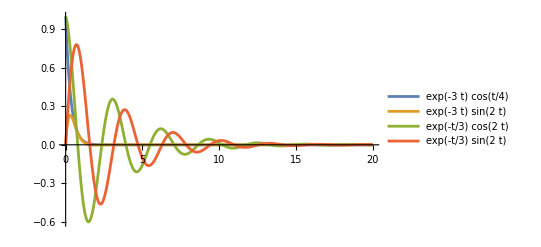

```mathematica
Plot[{Exp[σ1 t]Cos[ω1 t],Exp[σ1 t]Sin[ω2 t],Exp[σ2 t]Cos[ω2 t],Exp[σ2 t]Sin[ω2 t]}, {t,0,20},PlotRange->All, PlotLegends->"Expressions"]
```

Il grafico conferma la convergenza a zero dei modi, come assunto precedentemente.

## 2. Risposta libera

Determinare la risposta libera nello stato del sistema, equivale a studiare il suo comportamento nella configurazione in cui: l’ingresso è nullo e lo stato iniziale è assegnato e noto. La risposta libera nello stato per un sistema LTI-TC è pari a: .
Dunque, posso anche calcolare la risposta libera nello stato utilizzando , cioè lo stato iniziale  proiettato lungo le colonne di , ovvero della matrice di cambiamento di base, e la matrice di Rotation-Scaling .

```mathematica
={{0},{-2},{3},{-2}}
```

{{0},{-2},{3},{-2}}

Calcolo della risposta libera come per definizione, cioè . Non essendo lo stato combinazione lineare di nessuna delle colonne della matrice di cambiamento di base, nell’espansione modale della risposta libera mi aspetto che compaiano tutti i modi naturali del sistema.

```mathematica
[t_]:=Expand[Simplify[MatrixExp[A t].]]
```

```mathematica
[t]// MatrixForm
```

((31761999 ⅇ^(-3 t) Cos[t/4])/2568145-(31761999 ⅇ^(-t/3) Cos[2 t])/2568145-(1472190137 ⅇ^(-3 t) Sin[t/4])/10272580-(372104693 ⅇ^(-t/3) Sin[2 t])/23113305
-(28657472 ⅇ^(-3 t) Cos[t/4])/2568145+(23521182 ⅇ^(-t/3) Cos[2 t])/2568145-(207507256 ⅇ^(-3 t) Sin[t/4])/2568145-(7991314 ⅇ^(-t/3) Sin[2 t])/2568145
-(12853166 ⅇ^(-3 t) Cos[t/4])/2568145+(20557601 ⅇ^(-t/3) Cos[2 t])/2568145+(265900552 ⅇ^(-3 t) Sin[t/4])/2568145-(151125371 ⅇ^(-t/3) Sin[2 t])/7704435
(26323869 ⅇ^(-3 t) Cos[t/4])/2568145-(31460159 ⅇ^(-t/3) Cos[2 t])/2568145-(3160905657 ⅇ^(-3 t) Sin[t/4])/10272580+(99224467 ⅇ^(-t/3) Sin[2 t])/23113305)

Proprio come aspettato compaiono tutti i modi naturali. Verifico il risultato calcolando la risposta libera a partire dalla matrice di cambiamento di base che genera la matrice di Rotation-Scaling, infatti partendo dalla relazione , si ottiene che la matrice di Rotation-Scaling è pari a .
Per semplicità di calcoli riutilizzo la matrice di cambiamento di base T, calcolata in precedenza cambiando la sua nomenclatura con .

```mathematica
T̂ = T
```

{{583099/1249755,-30808/1249755,3709/7585,-11268/7585},{108768/416585,56192/1249755,-5652/7585,54/7585},{-420736/1249755,2104/416585,-1641/1517,-1854/1517},{1,0,1,0}}

```mathematica
MatrixForm[]
```

(583099/1249755 | -30808/1249755 | 3709/7585 | -11268/7585
108768/416585 | 56192/1249755 | -5652/7585 | 54/7585
-420736/1249755 | 2104/416585 | -1641/1517 | -1854/1517
1 | 0 | 1 | 0)

Proietto lo stato iniziale lungo le colonne di

```mathematica
=Inverse[T̂].
```

{{26323869/2568145},{-3160905657/10272580},{-31460159/2568145},{99224467/23113305}}

Calcolo la matrice di Rotation-Scaling

```mathematica
=Λ
```

{{-3,1/4,0,0},{-1/4,-3,0,0},{0,0,-1/3,2},{0,0,-2,-1/3}}

```mathematica
MatrixForm[]
```

(-3 | 1/4 | 0 | 0
-1/4 | -3 | 0 | 0
0 | 0 | -1/3 | 2
0 | 0 | -2 | -1/3)

Calcolo la risposta libera nello stato tramite matrice di Rotation-Scaling e

```mathematica
[t_]:=Expand[Simplify[T̂.MatrixExp[ t].]]
```

```mathematica
[t]// MatrixForm
```

((31761999 ⅇ^(-3 t) Cos[t/4])/2568145-(31761999 ⅇ^(-t/3) Cos[2 t])/2568145-(1472190137 ⅇ^(-3 t) Sin[t/4])/10272580-(372104693 ⅇ^(-t/3) Sin[2 t])/23113305
-(28657472 ⅇ^(-3 t) Cos[t/4])/2568145+(23521182 ⅇ^(-t/3) Cos[2 t])/2568145-(207507256 ⅇ^(-3 t) Sin[t/4])/2568145-(7991314 ⅇ^(-t/3) Sin[2 t])/2568145
-(12853166 ⅇ^(-3 t) Cos[t/4])/2568145+(20557601 ⅇ^(-t/3) Cos[2 t])/2568145+(265900552 ⅇ^(-3 t) Sin[t/4])/2568145-(151125371 ⅇ^(-t/3) Sin[2 t])/7704435
(26323869 ⅇ^(-3 t) Cos[t/4])/2568145-(31460159 ⅇ^(-t/3) Cos[2 t])/2568145-(3160905657 ⅇ^(-3 t) Sin[t/4])/10272580+(99224467 ⅇ^(-t/3) Sin[2 t])/23113305)

Come volevasi verificare i risultati sono i medesimi.

Verifica esaustiva per accertarsi che il risultato sia corretto è che la risposta libera converga a 0, componente per componente.

```mathematica
Limit[[t], t ->∞]
```

{{0},{0},{0},{0}}

La risposta libera nell’uscita è pari al prodotto tra la matrice di uscita C e la risposta libera nello stato:

```mathematica
[t_]:=Expand[Simplify[C1.[t]]]
```

```mathematica
[t]
```

{{(31098528 ⅇ^(-3 t) Cos[t/4])/2568145-(7985223 ⅇ^(-t/3) Cos[2 t])/2568145+(153686784 ⅇ^(-3 t) Sin[t/4])/2568145+(29958291 ⅇ^(-t/3) Sin[2 t])/2568145}}

Grafico della risposta libera nell’uscita

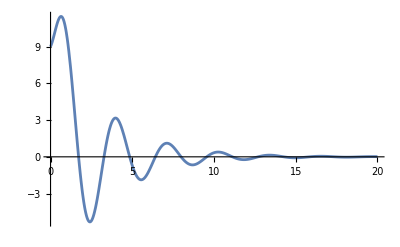

```mathematica
Plot[[t],{t,0,20},PlotRange->All]
```

## 3. Studio della configurazione degli stati iniziali che attivano sulla risposta libera alcuni modi naturali ed altri no

La risposta libera nello stato è una combinazione lineare dipendente dai modi naturali del sistema, perciò scegliendo un particolare stato iniziale che è “allineato” lungo la direzione di un autovalore, sulla risposta libera si accenderanno solo i modi associati a quell’autovalore. Se invece scegliessi combinazioni lineari dei modi naturali, si attiverebbero solo i modi presenti in quella combinazione lineare. Operativamente, si pone come stato iniziale una combinazione lineare delle colonne della matrice T relative agli stato che voglio visualizzare. Analizzo la configurazione che attiva i modi naturali corrispondenti alla coppia di autovalori -3+ⅈ/4,-3-ⅈ/4.

```mathematica
=1/2[[All,1]]+1/2[[All,2]]
```

{184097/833170,191248/1249755,-207212/1249755,1/2}

```mathematica
[t_]:=Expand[Simplify[MatrixExp[A t].]]
```

```mathematica
MatrixForm[[t]]
```

((184097 ⅇ^(-3 t) Cos[t/4])/833170+(613907 ⅇ^(-3 t) Sin[t/4])/2499510
(191248 ⅇ^(-3 t) Cos[t/4])/1249755+(135056 ⅇ^(-3 t) Sin[t/4])/1249755
-(207212 ⅇ^(-3 t) Cos[t/4])/1249755-(213524 ⅇ^(-3 t) Sin[t/4])/1249755
1/2 ⅇ^(-3 t) Cos[t/4]+1/2 ⅇ^(-3 t) Sin[t/4])

Verifico proiettando lo stato lungo le colonne di

```mathematica
=Inverse[].
```

{1/2,1/2,0,0}

```mathematica
[t_]:=Expand[Simplify[T̂.MatrixExp[ t].]]
```

```mathematica
[t] //MatrixForm
```

((184097 ⅇ^(-3 t) Cos[t/4])/833170+(613907 ⅇ^(-3 t) Sin[t/4])/2499510
(191248 ⅇ^(-3 t) Cos[t/4])/1249755+(135056 ⅇ^(-3 t) Sin[t/4])/1249755
-(207212 ⅇ^(-3 t) Cos[t/4])/1249755-(213524 ⅇ^(-3 t) Sin[t/4])/1249755
1/2 ⅇ^(-3 t) Cos[t/4]+1/2 ⅇ^(-3 t) Sin[t/4])

Come volevasi verificare. Analizzo adesso la configurazione che attiva i modi naturali corrispondenti alla coppia di autovalori 1/3+2 ⅈ,-1/3-2 ⅈ

```mathematica
= 5[[All,3]]+3[[All,4]]
```

{-15259/7585,-28098/7585,-13767/1517,5}

```mathematica
[t_]:=Expand[Simplify[MatrixExp[A t].]]
```

```mathematica
MatrixForm[[t]]
```

(-(15259 ⅇ^(-t/3) Cos[2 t])/7585+(67467 ⅇ^(-t/3) Sin[2 t])/7585
-(28098 ⅇ^(-t/3) Cos[2 t])/7585-(17226 ⅇ^(-t/3) Sin[2 t])/7585
-(13767 ⅇ^(-t/3) Cos[2 t])/1517+(4347 ⅇ^(-t/3) Sin[2 t])/1517
5 ⅇ^(-t/3) Cos[2 t]+3 ⅇ^(-t/3) Sin[2 t])

Anche in questo caso verifico proiettando lo stato lungo le colonne di

```mathematica
=Inverse[].
```

{0,0,5,3}

```mathematica
[t_]:=Expand[Simplify[T̂.MatrixExp[ t].]]
```

```mathematica
[t] //MatrixForm
```

(-(15259 ⅇ^(-t/3) Cos[2 t])/7585+(67467 ⅇ^(-t/3) Sin[2 t])/7585
-(28098 ⅇ^(-t/3) Cos[2 t])/7585-(17226 ⅇ^(-t/3) Sin[2 t])/7585
-(13767 ⅇ^(-t/3) Cos[2 t])/1517+(4347 ⅇ^(-t/3) Sin[2 t])/1517
5 ⅇ^(-t/3) Cos[2 t]+3 ⅇ^(-t/3) Sin[2 t])

Come volevasi dimostrare.

## 4. Funzione di trasferimento, i suoi poli e zeri

La funzione di trasferimento di un sistema LTI-TC è quella funzione di variabile complessa  tale che moltiplicata algebricamente per la L-Trasformata dell’ingresso restituisce la L-Trasformata della risposta forzata. È definita come , ovvero il rapporto tra L-Trasformata della risposta forzata e L-Trasformata dell’ingresso. Esplicitando la L-Trasformata della risposta forzata come:  la funzione di trasferimento è pari a . Nel caso di sistema proprio, .

```mathematica
G[s_]:=Simplify[C1.Inverse[s IdentityMatrix[4]-A].B]
```

```mathematica
G[s]
```

{{432/(5365+4422 s+2473 s^2+960 s^3+144 s^4)}}

Un polo è un numero complesso ρ tale che: , inoltre i poli sono le radici del denominatore della funzione di trasferimento ed anche un sottoinsieme dello spettro di A.
Uno zero è un numero complesso ζ  tale che: , dunque gli zeri rappresentano le radici del numeratore della funzione di trasferimento.

```mathematica
PoliFdt=Solve[Denominator[G[s]]==0,s]
```

{{s→-3-ⅈ/4},{s→-3+ⅈ/4},{s→-1/3-2 ⅈ},{s→-1/3+2 ⅈ}}

In questo caso i poli coincidono con gli autovalori di A

```mathematica
ZeriFdt=Solve[Numerator[G[s]]==0,s]
```

{}

Verifico i calcoli tramite funzioni built-in di Mathematica

```mathematica
Σ=StateSpaceModel[{A,B,C1}]
```

9403/2883847/144-2933/72-10747/2881/21-10-102-1-1008827/2883847/144-2789/72-10747/2881/2-3-3330StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionModel[Σ]
```

3/(5365/144+(737 s)/24+(2473 s^2)/144+(20 s^3)/3+s^4)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11353651FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionPoles[Σ][[1,1]]
```

{-3-ⅈ/4,-3+ⅈ/4,-1/3-2 ⅈ,-1/3+2 ⅈ}

```mathematica
TransferFunctionZeros[Σ]
```

{{{}}}

Come volevasi verificare i risultati sono corretti.

## 5. Risposta al gradino unitario

### 5.1 Calcolo risposta al gradino unitario

Il gradino unitario è un segnale di tipo polinomiale, right-sided definito tramite notazione piecewise: Piecewise[{{1, t}, {0, t < 0}}]. Per determinare la risposta al gradino unitario, si utilizzerà la risposta forzata, che è pari al prodotto tra funzione di trasferimento e la L-Trasformata dell’ingresso. In questo caso l’ingresso è il gradino unitario quindi si utilizzerà la L-Trasformata del gradino unitario pari a , ricavata dalla L-Trasformata dell’esponenziale, considerando : .

```mathematica
U[s]=LaplaceTransform[1,t,s]
```

1/s

```mathematica
[s_]:=G[s]U[s]
```

```mathematica
[s]
```

{{432/(s (5365+4422 s+2473 s^2+960 s^3+144 s^4))}}

La risposta forzata ottenuta è però nel dominio della variabile complessa  e non nel dominio del tempo. Per ottenere la risposta forzata nel dominio del tempo, occorre antitrasformare il risultato ottenuto. Dato che la risposta forzata è esprimibile come combinazione lineare del contributo dell’ingresso più la combinazione lineare dei modi naturali, si utilizzerà la scomposizione in fratti semplici e la formula elementare di Heaviside per passare al dominio del tempo. La scomposizione in fratti semplici in questo caso oltre a considerare i poli della funzione di trasferimento, considera un polo aggiuntivo legato all’ingresso pari a .
La formula elementare di Heaviside è pari a:  dove l’i-esimo coefficiente  è pari a: .
La scomposizione in fratti semplici risulta essere la seguente:

```mathematica
fs=/s+/(s+3+ⅈ/4)+/(s+3-ⅈ/4)+/(s+1/3+2 ⅈ)+/(s+1/3-2 ⅈ)
```

C_1/s+C_2/((3+ⅈ/4)+s)+C_3/((3-ⅈ/4)+s)+C_4/((1/3-2 ⅈ)+s)+C_4/((1/3+2 ⅈ)+s)

```mathematica
=Limit[s[s], s ->0]
```

{{432/5365}}

```mathematica
=Limit[(s+3+ⅈ/4)[s], s ->-3-ⅈ/4]
```

{{-2692224/74476205-(2612736 ⅈ)/14895241}}

```mathematica
=Limit[(s+3-ⅈ/4)[s], s ->-3+ⅈ/4]
```

{{-2692224/74476205+(2612736 ⅈ)/14895241}}

```mathematica
=Limit[(s+1/3+2 ⅈ)[s], s ->-1/3-2 ⅈ]
```

{{-390744/95021365-(3134052 ⅈ)/95021365}}

```mathematica
=Limit[(s+1/3-2 ⅈ)[s], s ->-1/3+2 ⅈ]
```

{{-390744/95021365+(3134052 ⅈ)/95021365}}

```mathematica
fs
```

{{432/(5365 s)-(390744/95021365+(3134052 ⅈ)/95021365)/((1/3-2 ⅈ)+s)-(390744/95021365+(3134052 ⅈ)/95021365)/((1/3+2 ⅈ)+s)-(2692224/74476205-(2612736 ⅈ)/14895241)/((3-ⅈ/4)+s)-(2692224/74476205+(2612736 ⅈ)/14895241)/((3+ⅈ/4)+s)}}

Ricordando di nuovo che la L-Trasformata dell’esponenziale è: , passo al dominio del tempo con le antitrasformate dei singoli addendi della scomposizione.

,  ,  ,  , 
La risposta forzata nel dominio del tempo sarà:

```mathematica
[t_]:=UnitStep[t]+Exp[(-3-ⅈ/4)t]UnitStep[t]+Exp[(-3+ⅈ/4)t]UnitStep[t]+Exp[(-1/3-2 ⅈ) t]UnitStep[t]+Exp[(-1/3+2 ⅈ )t]UnitStep[t]
```

```mathematica
[t]
```

{{(432 UnitStep[t])/5365-(2692224/74476205+(2612736 ⅈ)/14895241) ⅇ^((-3-ⅈ/4) t) UnitStep[t]-(2692224/74476205-(2612736 ⅈ)/14895241) ⅇ^((-3+ⅈ/4) t) UnitStep[t]-(390744/95021365+(3134052 ⅈ)/95021365) ⅇ^((-1/3-2 ⅈ) t) UnitStep[t]-(390744/95021365-(3134052 ⅈ)/95021365) ⅇ^((-1/3+2 ⅈ) t) UnitStep[t]}}

Si può verificare il risultato attraverso funzione antitrasformata di Laplace di Mathematica

```mathematica
[t_]:=Expand[InverseLaplaceTransform[[s],s,t]]
```

```mathematica
[t]
```

{{432/5365-(2692224/74476205+(2612736 ⅈ)/14895241) ⅇ^((-3-ⅈ/4) t)-(2692224/74476205-(2612736 ⅈ)/14895241) ⅇ^((-3+ⅈ/4) t)-(390744/95021365+(3134052 ⅈ)/95021365) ⅇ^((-1/3-2 ⅈ) t)-(390744/95021365-(3134052 ⅈ)/95021365) ⅇ^((-1/3+2 ⅈ) t)}}

Tuttavia la risposta forzata è combinazione lineare di termini reali. I termini complessi e coniugati della risposta forzata nel dominio del tempo devono essere convertiti in reali.

```mathematica
=Simplify[ComplexExpand[ⅇ^((-3-ⅈ/4)t)+ⅇ^((-3+ⅈ/4)t)]]
```

{{-(6912 ⅇ^(-3 t) (779 Cos[t/4]+3780 Sin[t/4]))/74476205}}

```mathematica
=Simplify[ComplexExpand[ⅇ^((-1/3-2 ⅈ)t)+ⅇ^((-1/3+2 ⅈ)t)]]
```

{{-(648 ⅇ^(-t/3) (1206 Cos[2 t]+9673 Sin[2 t]))/95021365}}

In definitiva la risposta al gradino unitario nel dominio del tempo è:

```mathematica
[t_]:=++
```

```mathematica
[t]
```

{{432/5365-(6912 ⅇ^(-3 t) (779 Cos[t/4]+3780 Sin[t/4]))/74476205-(648 ⅇ^(-t/3) (1206 Cos[2 t]+9673 Sin[2 t]))/95021365}}

Grafico della risposta al gradino unitario

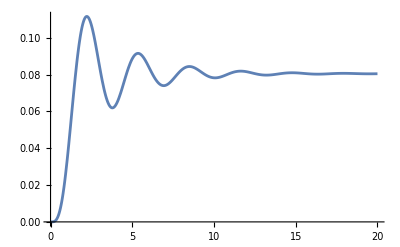

```mathematica
Plot[[t],{t,0,20},PlotRange->All]
```

### 5.2 Scomposizione risposta

La risposta forzata è composta da: risposta a regime o steady state response, che descrive il valore a cui la risposta forzata convergere e risposta transitoria, presente solo se i modi naturali convergono. 
La risposta a regime è pari al contributo dato dall’ingresso, ottenuto prendendo il gradino unitario e scalandolo di un fattore, interpretato come fattore di distorsione sul gradino. La risposta a regime è definita come segue:  che in questo caso coincide con  che sarà il fattore di distorsione.

```mathematica
RispRegime=
```

{{432/5365}}

La risposta transitoria è data in questo caso, dagli ultimi quattro termini della risposta al gradino unitario.

```mathematica
RispTransitoria=[t]-
```

{{-(6912 ⅇ^(-3 t) (779 Cos[t/4]+3780 Sin[t/4]))/74476205-(648 ⅇ^(-t/3) (1206 Cos[2 t]+9673 Sin[2 t]))/95021365}}

La risposta transitoria è tale perché si esaurisce nel tempo per . Infatti si può verificare che il limite per  , della risposta transitoria è pari a zero

```mathematica
Limit[RispTransitoria,t->∞]
```

{{0}}

Grafico dellla risposta forzata evidenziando la risposta a regime e la risposta transitoria.

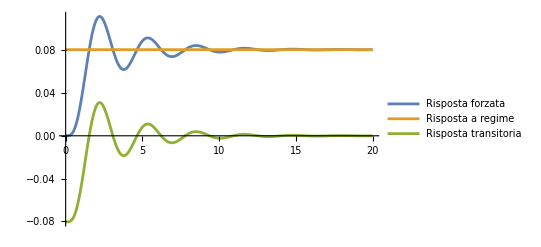

```mathematica
Plot[{[t],RispRegime,RispTransitoria},{t,0,20},PlotRange->All, PlotLegends->{"Risposta forzata", "Risposta a regime", "Risposta transitoria"}]
```

## 6. Risposta al segnale periodico elementare

### 6.1 Calcolo della risposta al segnale periodico elementare

Come nel caso del gradino unitario, per determinare la risposta al segnale periodico elementare, si utilizzerà la risposta forzata, valutando per ingresso il segnale periodico. 
La L-Trasformata del segnale periodico elementare seno è pari a: . Per semplificare i calcoli scelgo la seguente terna  affinché la L-Trasformata del segnale sarà .

```mathematica
[s_]:=LaplaceTransform[Sin[t]UnitStep[t],t,s]
```

```mathematica
[s]
```

1/(1+s^2)

Calcolo la risposta forzata nel dominio della variabile complessa

```mathematica
[s_]:=G[s][s]
```

```mathematica
[s]
```

{{432/((1+s^2) (5365+4422 s+2473 s^2+960 s^3+144 s^4))}}

Anche in questo caso si utilizza la scomposizione in fratti semplici e la formula elementare di Heaviside per ritornare nel dominio del tempo.

```mathematica
/(s+ⅈ)+/(s-ⅈ)+/(s+3+ⅈ/4)+/(s+3-ⅈ/4)+/(s+1/3+2 ⅈ)+/(s+1/3-2 ⅈ)
```

D_1/(ⅈ+s)+D_2/(-ⅈ+s)+D_3/((3+ⅈ/4)+s)+D_4/((3-ⅈ/4)+s)+D_5/((1/3+2 ⅈ)+s)+D_6/((1/3-2 ⅈ)+s)

A differenza del gradino unitario, in questo caso i fratti semplici sono sei, i primi due quali sono legati dall’ingresso ed i restanti quattro sono legati dai modi naturali. I coefficienti sono calcolati nel medesimo modo visto in precedenza per il gradino unitario.

```mathematica
=Limit[(s+ⅈ)[s], s ->-ⅈ]
```

{{-20772/588965+(18216 ⅈ)/588965}}

```mathematica
=Limit[(s-ⅈ)[s], s ->ⅈ]
```

{{-20772/588965-(18216 ⅈ)/588965}}

```mathematica
=Limit[(s+3+ⅈ/4)[s], s ->-3-ⅈ/4]
```

{{105541632/7378280585+(381482496 ⅈ)/7378280585}}

```mathematica
=Limit[(s+3-ⅈ/4)[s], s ->-3+ⅈ/4]
```

{{105541632/7378280585-(381482496 ⅈ)/7378280585}}

```mathematica
=Limit[(s+1/3+2 ⅈ)[s], s ->-1/3-2 ⅈ]
```

{{2207412/105293945+(63666 ⅈ)/21058789}}

```mathematica
=Limit[(s+1/3-2 ⅈ)[s], s ->-1/3+2 ⅈ]
```

{{2207412/105293945-(63666 ⅈ)/21058789}}

```mathematica
(1/(s+ⅈ))+(1/(s-ⅈ))+(1/(s+3+ⅈ/4))+(1/(s+3-ⅈ/4))+(1/(s+1/3+2 ⅈ))+(1/(s+1/3-2 ⅈ))
```

{{-(20772/588965+(18216 ⅈ)/588965)/(-ⅈ+s)-(20772/588965-(18216 ⅈ)/588965)/(ⅈ+s)+(2207412/105293945-(63666 ⅈ)/21058789)/((1/3-2 ⅈ)+s)+(2207412/105293945+(63666 ⅈ)/21058789)/((1/3+2 ⅈ)+s)+(105541632/7378280585-(381482496 ⅈ)/7378280585)/((3-ⅈ/4)+s)+(105541632/7378280585+(381482496 ⅈ)/7378280585)/((3+ⅈ/4)+s)}}

Utilizzo la L-Trasformata dell’esponenziale è:  per passare al dominio del tempo.
,  ,  ,  , 
Termini reali per costruire la risposta

```mathematica
=Simplify[ComplexExpand[ⅇ^(-ⅈ t)+ⅇ^(ⅈ t)]]
```

{{-(72 (577 Cos[t]-506 Sin[t]))/588965}}

```mathematica
=Simplify[ComplexExpand[ⅇ^((-3-ⅈ/4)t)+ⅇ^((-3+ⅈ/4)t)]]
```

{{(9216 ⅇ^(-3 t) (22904 Cos[t/4]+82787 Sin[t/4]))/7378280585}}

```mathematica
=Simplify[ComplexExpand[ⅇ^((-1/3-2 ⅈ)t)+ⅇ^((-1/3+2 ⅈ)t)]]
```

{{(972 ⅇ^(-t/3) (4542 Cos[2 t]+655 Sin[2 t]))/105293945}}

```mathematica
[t_]:=UnitStep[t]+UnitStep[t]+UnitStep[t]
```

```mathematica
[t]
```

{{(9216 ⅇ^(-3 t) (22904 Cos[t/4]+82787 Sin[t/4]) UnitStep[t])/7378280585-(72 (577 Cos[t]-506 Sin[t]) UnitStep[t])/588965+(972 ⅇ^(-t/3) (4542 Cos[2 t]+655 Sin[2 t]) UnitStep[t])/105293945}}

Grafico della risposta al segnale periodico elementare

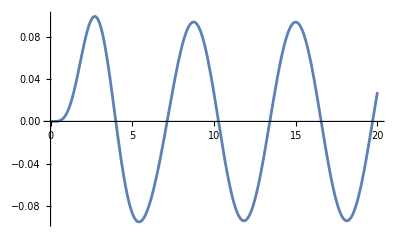

```mathematica
Plot[[t],{t,0,20},PlotRange->All]
```

### 6.2 Scomposizione della risposta

La risposta a regime è pari a:  con  coefficiente legato all’ingresso. Uso la forma Amplitude-Fase per determinare la coppia ampiezza-fase della risposta a regime

```mathematica
RispRegimePerio=ComplexExpand[2Re[ⅇ^(ⅈ t)]]
```

{{-(41544 Cos[t])/588965+(36432 Sin[t])/588965}}

Devo determinare   tale che -(41544 Cos[t])/588965+(36432 Sin[t])/588965=X Sin(t+ϕ)

```mathematica
AmpF=RispRegimePerio== X Sin[t + ϕ]
```

{{-(41544 Cos[t])/588965+(36432 Sin[t])/588965}}==X Sin[t+ϕ]

Ho un’equazione e due incognite, spezzo perciò l’equazione in due: nella prima valutoil tutto per  e nella seconda valuto le rispettive derivate per

```mathematica
Solve[{(AmpF) /. {t->0}, (D[-(41544 Cos[t])/588965+(36432 Sin[t])/588965,t]==D[X Sin[t+ϕ],t]) /. {t->0}, X >0}, {X,ϕ}]
```

{{X→ConditionalExpression[72/(13 √3485), C[1]∈ℤ],ϕ→ConditionalExpression[2 ArcTan[(-45305+506 √3485)/(577 √3485)]+2 π C[1], C[1]∈ℤ]}}

Trasformo la coppia ampiezza fase in decimale

```mathematica
N[72/(13 √3485)]
```

0.0938183

```mathematica
N[2 ArcTan[(-45305+506 √3485)/(577 √3485)]](180/π)
```

-48.7509

Dato che <0 si ha un ritardo di fase. Procedo infine con il grafico della risposta forzata e della risposta a regime per visualizzare tale ritardo.

```mathematica
[t_]:=++
```

```mathematica
[t]
```

{{(9216 ⅇ^(-3 t) (22904 Cos[t/4]+82787 Sin[t/4]))/7378280585-(72 (577 Cos[t]-506 Sin[t]))/588965+(972 ⅇ^(-t/3) (4542 Cos[2 t]+655 Sin[2 t]))/105293945}}

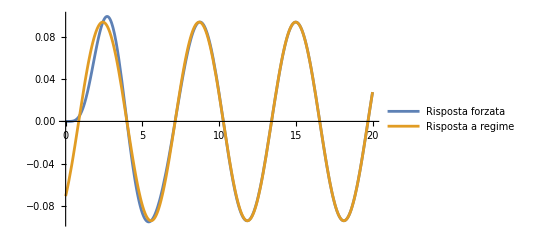

```mathematica
Plot[{[t],RispRegimePerio}, {t,0,20}, PlotRange->All, PlotLegends->{"Risposta forzata", "Risposta a regime"}]
```

Da notare anche come la risposta transitoria scompaia molto rapidamente.

## 7. Modello ARMA e risposta alla rampa unitaria

### 7.1 Modello ARMA

Occorre adesso determinare il modello ARMA equivalente, individuando le condizioni iniziali sull’uscita compatibili con lo stato iniziale .

```mathematica
={{3},{-3},{-1},{2}}
```

{{3},{-3},{-1},{2}}

Per determinare il modello ARMA, occorre valutare il sistema dinamico nella rappresentazione Ingresso-Uscita. Rispetto alla rappresentazione Ingresso-Stato-Uscita, per  equivalente, qualsiasi sia l’ingresso, con condizioni iniziali nulle, l’uscita forzata corrispondente è la stessa a parità di ingresso. Ciò vale anche per la risposta libera e risposta forzata a patto che ci siano le stesse condizioni iniziali. 
Per prima cosa si valuta la funzione di trasferimento come un’identità dunque: 432/(5365+4422 s+2473 s^2+960 s^3+144 s^4)=(Y(s))/(U(s)) da cui attraverso operazioni algebriche si ottiene la seguente equazione:

```mathematica
id=Expand[Denominator[G[s]]Yar[s]]==Expand[Numerator[G[s]]Uar[s]]
```

{{5365 Yar[s]+4422 s Yar[s]+2473 s^2 Yar[s]+960 s^3 Yar[s]+144 s^4 Yar[s]}}=={{432 Uar[s]}}

L’equazione è nel dominio della variabile complessa  e va riportata nel dominio del tempo, attraverso l’antitrasformata di Laplace. 
In particolare si sfrutta l’estensione del teorema della derivata per la  L-Trasformata, che consente di valutare la L-Trasformata della derivata di ordine  di una funzione: .
Nel caso in oggetto: , , , . Per  passare da una rappresentazione Ingresso-Stato-Uscita, ad una rappresentazione Ingresso-Uscita, è necessario che le condizioni iniziali sulla risposta forzata siano nulle:  .

```mathematica
InverseLaplaceTransform[id,s,t] /. {Yar[s]->LaplaceTransform[yar[t],t,s],Uar[s]->LaplaceTransform[uar[t],t,s]} /. { yar[0]-> 0, yar'[0]-> 0, yar''[0]-> 0, yar'''[0]-> 0, yar''''[0]-> 0, uar[0]-> 0}
```

{{5365 yar[t]+4422 yar'[t]+2473 yar''[t]+960 yar^(3)[t]+144 yar^(4)[t]}}=={{432 uar[t]}}

L’equazione differenziale costruita, presenta solo l’ingresso e l’uscita e ho dunque la rappresentazione Ingresso-Uscita del sistema.

```mathematica
EqDiff=5365 yar[t]+4422 yar'[t]+2473 yar''[t]+960 Derivative[3][yar][t]+144 Derivative[4][yar][t]==432 uar[t]
```

5365 yar[t]+4422 yar'[t]+2473 yar''[t]+960 yar^(3)[t]+144 yar^(4)[t]==432 uar[t]

A questo punto risolvo l’equazione differenziale nel dominio della variabile complessa

```mathematica
EqDiffs=LaplaceTransform[EqDiff,t,s] /. {yar[t]->InverseLaplaceTransform[Yar[s],s,t],uar[t]->InverseLaplaceTransform[Uar[s],s,t]}
```

5365 Yar[s]+4422 (-yar[0]+s Yar[s])+2473 (-s yar[0]+s^2 Yar[s]-yar'[0])+960 (-s^2 yar[0]+s^3 Yar[s]-s yar'[0]-yar''[0])+144 (-s^3 yar[0]+s^4 Yar[s]-s^2 yar'[0]-s yar''[0]-yar^(3)[0])==432 Uar[s]

```mathematica
Risposta=Collect[Solve[EqDiffs,Yar[s]][[1,1]][[2]],Uar[s]]
```

(432 Uar[s])/(5365+4422 s+2473 s^2+960 s^3+144 s^4)+(4422 yar[0]+2473 s yar[0]+960 s^2 yar[0]+144 s^3 yar[0]+2473 yar'[0]+960 s yar'[0]+144 s^2 yar'[0]+960 yar''[0]+144 s yar''[0]+144 yar^(3)[0])/(5365+4422 s+2473 s^2+960 s^3+144 s^4)

```mathematica
Libera=Collect[Solve[EqDiffs,Yar[s]][[1,1]][[2]],Uar[s]][[2]]
```

(4422 yar[0]+2473 s yar[0]+960 s^2 yar[0]+144 s^3 yar[0]+2473 yar'[0]+960 s yar'[0]+144 s^2 yar'[0]+960 yar''[0]+144 s yar''[0]+144 yar^(3)[0])/(5365+4422 s+2473 s^2+960 s^3+144 s^4)

Per calcolare la risposta libera mi occorrono altre quattro condizioni iniziali sull’uscita:  .

```mathematica
yfar[0]=C1.
```

{{3}}

```mathematica
yfar'[0]=C1.A.
```

{{-6}}

```mathematica
yfar''[0]=C1.A.A.
```

{{6}}

```mathematica
yfar'''[0]=C1.A.A.A.
```

{{18}}

```mathematica
Yliberas [s_]:=Libera
```

```mathematica
Yliberas[s]
```

(6780+2523 s+2016 s^2+432 s^3)/(5365+4422 s+2473 s^2+960 s^3+144 s^4)

Riporto nel dominio del tempo la risposta libera nel dominio della variabile complessa  tramite l’antitrasformata di Laplace

```mathematica
Ylibera[t_]:=FullSimplify[InverseLaplaceTransform[Yliberas[s],s,t]]
```

```mathematica
Ylibera[t]
```

(3 ⅇ^(-3 t) (5162912 Cos[t/4]+24377216 Sin[t/4]-9 ⅇ^(8 t/3) (2958 Cos[2 t]+49279 Sin[2 t])))/5136290

Verifico con un confronto tra rappresentazione Ingresso-Stato-Uscita e rappresentazione Ingresso-Uscita

```mathematica
YISU[t_]:= InverseLaplaceTransform[C1.Inverse[s IdentityMatrix[4]-A].,s,t]
```

```mathematica
YISU[t]
```

{{(24 ⅇ^((-3-ⅈ/4) t) ((161341+761788 ⅈ)+(161341-761788 ⅈ) ⅇ^((ⅈ t)/2)))/2568145-(27 ⅇ^((-1/3-2 ⅈ) t) ((2958+49279 ⅈ)+(2958-49279 ⅈ) ⅇ^(4 ⅈ t)))/10272580}}

```mathematica
FullSimplify[Ylibera[t]-YISU[t]]
```

{{0}}

Come volevasi verificare.

### 7.2 Risposta alla rampa unitaria

Procedo adesso a calcolare la risposta alla rampa unitaria, segnale polinomiale che può essere interpretato come velocità di variazione del segnale . La rampa unitaria è definita tramite notazione piecewise: Piecewise[{{t, }, {0, t<0}}]. La L-Trasformata della rampa unitaria pari si ottiene a partire da considerando  e  perciò .

```mathematica
[s]=LaplaceTransform[t UnitStep[t],t,s]
```

1/s^2

Calcolo la risposta forzata alla rampa unitaria, partendo dal modello ARMA ricavatomi

```mathematica
RispostaArmas=Solve[EqDiffs,Yar[s]][[1,1]] /. { yar[0]->3,  yar'[0]->-6,  yar''[0]->6,  yar'''[0]->18}
```

Yar[s]→(6780+2523 s+2016 s^2+432 s^3+432 Uar[s])/(5365+4422 s+2473 s^2+960 s^3+144 s^4)

Calcolo la risposta forzata alla rampa unitaria nel dominio del tempo tramite l’antitrasformata di Laplace

```mathematica
RispostaArmat=FullSimplify[ComplexExpand[InverseLaplaceTransform[(6780+2523 s+2016 s^2+432 s^3+432 Uar[s])/(5365+4422 s+2473 s^2+960 s^3+144 s^4) /. Uar[s] -> 1/s^2,s,t]]]
```

(3 (147925152 (-4422+5365 t)+43808 ⅇ^(-3 t) (686000633 Cos[t/4]+3228997196 Sin[t/4])+37845 ⅇ^(-t/3) (4481634 Cos[2 t]-67112023 Sin[2 t])))/29567798147050

Scompongo la risposta tramite la funzione Apart in risposta a regime e risposta transitoria

```mathematica
RispostaArma=Apart[RispostaArmat]
```

(432 (-4422+5365 t))/28783225+(48 ⅇ^(-3 t) (686000633 Cos[t/4]+3228997196 Sin[t/4]))/10799049725+(27 ⅇ^(-t/3) (4481634 Cos[2 t]-67112023 Sin[2 t]))/7031581010

```mathematica
RisRegimeRampa=RispostaArma[[1]]
```

(432 (-4422+5365 t))/28783225

La rispsota a regime è inoltre la componente legata algebricamente all’ingresso

```mathematica
RisTransitoriaRampa=RispostaArma-RisRegimeRampa
```

(48 ⅇ^(-3 t) (686000633 Cos[t/4]+3228997196 Sin[t/4]))/10799049725+(27 ⅇ^(-t/3) (4481634 Cos[2 t]-67112023 Sin[2 t]))/7031581010

Come verifica, procedo a calcolare la risposta alla rampa sfruttando la scomposizione in fratti semplici e la formula elementare di Heaviside

```mathematica
[s_]:=G[s][s]
```

```mathematica
[s]
```

{{432/(s^2 (5365+4422 s+2473 s^2+960 s^3+144 s^4))}}

Anche in questo caso i fratti semplici sono sei, i primi due quali sono legati dall’ingresso ed i restanti quattro sono legati dai modi naturali.

```mathematica
/s+/s^2+/(s+3+ⅈ/4)+/(s+3-ⅈ/4)+/(s+1/3+2 ⅈ)+/(s+1/3-2 ⅈ)
```

F_1/s+F_2/s^2+F_3/((3+ⅈ/4)+s)+F_4/((3-ⅈ/4)+s)+F_5/((1/3+2 ⅈ)+s)+F_6/((1/3-2 ⅈ)+s)

```mathematica
=Limit[D[s^2[s],s], s ->0]
```

{{-1910304/28783225}}

```mathematica
=Limit[s^2[s],s->0]
```

{{432/5365}}

```mathematica
=Limit[(s+3+ⅈ/4)[s], s ->-3-ⅈ/4]
```

{{181481472/10799049725+(616287744 ⅈ)/10799049725}}

```mathematica
=Limit[(s+3-ⅈ/4)[s], s ->-3+ⅈ/4]
```

{{181481472/10799049725-(616287744 ⅈ)/10799049725}}

```mathematica
=Limit[(s+1/3+2 ⅈ)[s], s ->-1/3-2 ⅈ]
```

{{57585168/3515790505+(2368764 ⅈ)/3515790505}}

```mathematica
=Limit[(s+1/3-2 ⅈ)[s], s ->-1/3+2 ⅈ]
```

{{57585168/3515790505-(2368764 ⅈ)/3515790505}}

Ne estraggo le parti reali

```mathematica
=Simplify[ComplexExpand[ⅇ^((-3-ⅈ/4)t)+ⅇ^((-3+ⅈ/4)t)]]
```

{{(27648 ⅇ^(-3 t) (13128 Cos[t/4]+44581 Sin[t/4]))/10799049725}}

```mathematica
=Simplify[ComplexExpand[ⅇ^((-1/3-2 ⅈ)t)+ⅇ^((-1/3+2 ⅈ)t)]]
```

{{(1944 ⅇ^(-t/3) (59244 Cos[2 t]+2437 Sin[2 t]))/3515790505}}

```mathematica
[t_]:=UnitStep[t]+t UnitStep[t]+UnitStep[t]+UnitStep[t]
```

```mathematica
[t]
```

{{-(1910304 UnitStep[t])/28783225+(432 t UnitStep[t])/5365+(27648 ⅇ^(-3 t) (13128 Cos[t/4]+44581 Sin[t/4]) UnitStep[t])/10799049725+(1944 ⅇ^(-t/3) (59244 Cos[2 t]+2437 Sin[2 t]) UnitStep[t])/3515790505}}

A meno di qualche manipolazione algebrica il risultato coincide con quello ottenuto precedentemente, una verifica di ciò è effettuabile attraverso la funzione Apart sulla risposta forzata

```mathematica
Apart[[t]]
```

{{(432 (-4422+5365 t) UnitStep[t])/28783225+(27648 ⅇ^(-3 t) (13128 Cos[t/4]+44581 Sin[t/4]) UnitStep[t])/10799049725+(1944 ⅇ^(-t/3) (59244 Cos[2 t]+2437 Sin[2 t]) UnitStep[t])/3515790505}}

## 8. Stato iniziale tale che la risposta al gradino coincida con il suo valore di regime

Per definizione la risposta è composta da risposta libera e risposta forzata e la risposta forzata, che a sua volta è composta da risposta a regime e risposta transitoria, dunque: 
risposta = risposta libera + risposta a regime + risposta transitoria. 
Affinché la risposta al gradino coincida con il suo valore di regime, è necessario che la risposta libera vada a compensare la risposta transitoria. Per individuare tale combinazione lineare, parto definendo il vettore stato iniziale

```mathematica
x0={{x1},{x2},{x3},{x4}}
```

{{x1},{x2},{x3},{x4}}

Calcolo risposta libera e risposta forzata

```mathematica
libera=Simplify[C1.Inverse[s IdentityMatrix[4]-A].x0][[1]][[1]]
```

(3 (-((6751+3433 s+1104 s^2+144 s^3) x1)-(5382+2617 s+960 s^2+144 s^3) x2+7711 x3+3577 s x3+1104 s^2 x3+144 s^3 x3+7039 x4+3433 s x4+1104 s^2 x4+144 s^3 x4))/(5365+4422 s+2473 s^2+960 s^3+144 s^4)

```mathematica
forzata= Simplify[G[s](1/s)][[1]][[1]]
```

432/(s (5365+4422 s+2473 s^2+960 s^3+144 s^4))

Calcolo la componente a regime della risposta al gradino

```mathematica
regime= (G[0](1/s))[[1]][[1]]
```

432/(5365 s)

Calcolo la risposta transitoria come risposta forzata - risposta a regime

```mathematica
transitoria=Factor[forzata-regime]
```

-(432 (4422+2473 s+960 s^2+144 s^3))/(5365 (37+6 s+9 s^2) (145+96 s+16 s^2))

Sommo libera e transitoria, ne estraggo il numeratore e lo pongo pari a zero

```mathematica
Numerator[Simplify[Expand[libera+transitoria]]]
```

-3 (636768+36219115 x1+28874430 x2-41369515 x3+s (356112+18418045 x1+14040205 x2-19190605 x3-18418045 x4)+240 s^2 (576+24679 x1+21460 x2-24679 x3-24679 x4)+144 s^3 (144+5365 x1+5365 x2-5365 x3-5365 x4)-37764235 x4)

Ho quattro incognite. Estraggo i coefficienti del polinomio al numeratore

```mathematica
CL=CoefficientList[Numerator[Simplify[Expand[libera+transitoria]]],s]
```

{-1910304-108657345 x1-86623290 x2+124108545 x3+113292705 x4,-3 (356112+18418045 x1+14040205 x2-19190605 x3-18418045 x4),-720 (576+24679 x1+21460 x2-24679 x3-24679 x4),-432 (144+5365 x1+5365 x2-5365 x3-5365 x4)}

Determino le incognite  che annullano il set dei coefficienti del polinomio al numeratore

```mathematica
Solve[CL== {0,0,0,0}, {x1,x2,x3,x4}]
```

{{x1→-144/5365,x2→-144/5365,x3→-144/5365,x4→0}}

Verifico il risultato ottenuto, calcolando la risposta a partire dallo stato iniziale ricavato

```mathematica
Σ1=StateSpaceModel[{A,B,C1}]
```

9403/2883847/144-2933/72-10747/2881/21-10-102-1-1008827/2883847/144-2789/72-10747/2881/2-3-3330StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Simplify[OutputResponse[{Σ1,{-144/5365,-144/5365,-144/5365,0}},1,t]]
```

{432/5365}

Come volevasi verificare si è ottenuta la risposta a regime

## 9. Risposta al segnale

Il calcolo della risposta al segnale  presuppone la BIBO stabilità o in generale l’asintotica stabilità. il sistema è asintotcamente stabile, dunque BIBO stabile perciò si può procedere al calcolo della risposta al segnale  . La risposta al segnale è definita tramite la notazione piecewise seguente: Piecewise[{{(t), }, {, t0}}] . Occorre perciò valutare la risposta per , pari alla risposta a regime e per  pari alla risposta libera. Infatti per la risposta è senza ingresso, ma tiene conto delle condizioni iniziali legate alla commutazione da uno a zero, dove in zero per continuità, valgono le seguenti relazioni: , , ... .
Per  la risposta è pari alla risposta a regime del gradino unitario

```mathematica
yneg=G[0][[1,1]]
```

432/5365

Per  mi ricavo lo stato iniziale a partire da: (y(0)


)=(C


) dove (C


)= è detta matrice d’osservabilità e da cui ricavo lo stato iniziale (


)

```mathematica
Obs={C1[[1]], (C1.A)[[1]],  (C1.A.A)[[1]], (C1.A.A.A)[[1]]}
```

{{-3,-3,3,3},{-3,0,3,3},{0,-3,3,0},{3,0,-3,3}}

```mathematica
= Inverse[Obs].{{G[0][[1,1]]},{0}, {0}, {0}}
```

{{-144/5365},{-144/5365},{-144/5365},{0}}

A questo punto posso calcolare la risposta per  tramire scomposizione in fratti semplici e formula elementare di Heaviside

```mathematica
ylibs=Simplify[(C1.Inverse[s IdentityMatrix[4]-A].)[[1,1]]]
```

(432 (4422+2473 s+960 s^2+144 s^3))/(5365 (5365+4422 s+2473 s^2+960 s^3+144 s^4))

```mathematica
/(s+3+ⅈ/4)+/(s+3-ⅈ/4)+/(s+1/3+2 ⅈ)+/(s+1/3-2 ⅈ)
```

H_1/((3+ⅈ/4)+s)+H_2/((3-ⅈ/4)+s)+H_3/((1/3+2 ⅈ)+s)+H_4/((1/3-2 ⅈ)+s)

```mathematica
=Limit[(s+3+ⅈ/4)ylibs, s ->-3-ⅈ/4]
```

2692224/74476205+(2612736 ⅈ)/14895241

```mathematica
=Limit[(s+3-ⅈ/4)ylibs, s ->-3+ⅈ/4]
```

2692224/74476205-(2612736 ⅈ)/14895241

```mathematica
=Limit[(s+1/3+2 ⅈ)ylibs,s ->-1/3-2 ⅈ]
```

390744/95021365+(3134052 ⅈ)/95021365

```mathematica
=Limit[(s+1/3-2 ⅈ)ylibs,s ->-1/3+2 ⅈ]
```

390744/95021365-(3134052 ⅈ)/95021365

```mathematica
=Simplify[ComplexExpand[ⅇ^((-3-ⅈ/4)t)+ⅇ^((-3+ⅈ/4)t)]]
```

(6912 ⅇ^(-3 t) (779 Cos[t/4]+3780 Sin[t/4]))/74476205

```mathematica
=Simplify[ComplexExpand[ⅇ^((-1/3-2 ⅈ)t)+ⅇ^((-1/3+2 ⅈ)t)]]
```

(648 ⅇ^(-t/3) (1206 Cos[2 t]+9673 Sin[2 t]))/95021365

```mathematica
ylib[t_]:=UnitStep[t]+UnitStep[t]
```

```mathematica
ylib[t]
```

(6912 ⅇ^(-3 t) (779 Cos[t/4]+3780 Sin[t/4]) UnitStep[t])/74476205+(648 ⅇ^(-t/3) (1206 Cos[2 t]+9673 Sin[2 t]) UnitStep[t])/95021365

```mathematica
FullSimplify[ylib[t]]
```

(216 ⅇ^(-3 t) (922336 Cos[t/4]+4475520 Sin[t/4]+87 ⅇ^(8 t/3) (1206 Cos[2 t]+9673 Sin[2 t])) UnitStep[t])/2755619585

Verifico la correttezza del risultato tramite antitrasformata di Laplace della risposta nel dominio della variabile complessa

```mathematica
ylibt=FullSimplify[ComplexExpand[InverseLaplaceTransform[ylibs,s,t]]]
```

(216 ⅇ^(-3 t) (922336 Cos[t/4]+4475520 Sin[t/4]+87 ⅇ^(8 t/3) (1206 Cos[2 t]+9673 Sin[2 t])))/2755619585

Combino le risposte per ottenere la risposta al segnale  e ne faccio il grafico.

```mathematica
y[t_]:=Piecewise[{{yneg, t<0}, {ylibt, t>=0}}]
```

```mathematica
y[t]
```

Piecewise[{{432/5365, t<0}, {(216 ⅇ^(-3 t) (922336 Cos[t/4]+4475520 Sin[t/4]+87 ⅇ^(8 t/3) (1206 Cos[2 t]+9673 Sin[2 t])))/2755619585, t≥0}, {0, True}}]

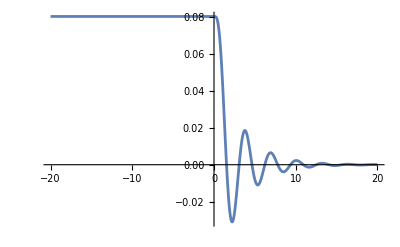

```mathematica
Plot[y[t],{t,-20,20},PlotRange->All]
```